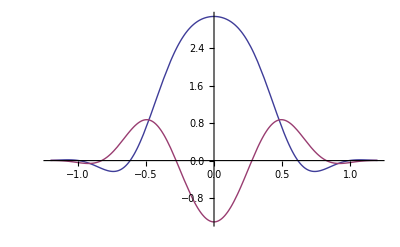

```mathematica
Plot[{Re[(3.08-I 1.31) Exp[-(4.39-I 5.20) q^2]],Im[(3.08-I 1.31) Exp[-(4.39-I 5.20) q^2]]},{q,-1.2,1.2}]
```

```mathematica
ppdat={{0.21,2.5-2.93 ⅈ,14.15-6.33 ⅈ},{0.21,2.42-3.11 ⅈ,15.6-7.1 ⅈ},{0.325,2.51-1.85 ⅈ,10.-10.53 ⅈ},{0.325,2.48-1.98 ⅈ,10.5-10.1 ⅈ},{0.425,2.78-1.53 ⅈ,6.68-8.73 ⅈ},{0.425,2.48-1.59 ⅈ,6.88-8.8 ⅈ},{0.508,3.08-1.31 ⅈ,4.39-5.2 ⅈ},{0.515,3.24-0.74 ⅈ,4.27-3.93 ⅈ},{0.515,3.22-1.41 ⅈ,5.35-6.78 ⅈ},{0.585,3.7-1.2 ⅈ,4.83-5.48 ⅈ},{0.585,3.7-1.09 ⅈ,3.77-4.16 ⅈ},{0.625,3.96-1.28 ⅈ,4.61-4.81 ⅈ},{0.665,4.25-0.88 ⅈ,4.65-4.38 ⅈ},{0.665,4.3-0.17 ⅈ,4.44-0.84 ⅈ},{0.73,4.63-0.61 ⅈ,4.6-3.65 ⅈ},{0.73,4.65+0.37 ⅈ,5.18+0.97 ⅈ},{0.831,4.88-0.17 ⅈ,4.33-2.79 ⅈ},{0.831,4.85+1.39 ⅈ,5.4+1.06 ⅈ},{0.917,4.86+0.91 ⅈ,4.83+0.77 ⅈ},{1,4.87+0.81 ⅈ,5.08+0.63 ⅈ},{1.18,4.87+1.01 ⅈ,4.59-0.43 ⅈ},{1.27,4.85+1.06 ⅈ,4.64-1.07 ⅈ},{1.73,4.7+1.86 ⅈ,4.4-0.55 ⅈ}};
```

```mathematica
pndat={{.210,4.18-I 2.70,10-I 5.66},{.210,4.42-I 3.64,16.44-I 4.54},{.325,3.58-I 1.04,10.1-I 9.60},{.325,3.82-I 1.15,10.10-I 9.94},{.425,3.41-I 0.47,6.25-I 8.23},{.425,3.40-I 0.13,6.09-I 5.97},{.515,3.47-I 0.20,4.77-I 6.40},{.515,3.33+I 0.61,4.74-I 3.58},{.585,3.57+I 0.02,4.25-I 5.24},{.665,3.70+I 0.29,4.01-I 4.22},{.730,3.80+I 0.49,3.94-I 3.51},{.831,3.83+I 0.78,3.77-I 2.59}};
```

```mathematica
ppA0rebf=BezierFunction[Transpose[{ppdat[[All,1]],Re[ppdat[[All,2]]]}]];
ppA0imbf=BezierFunction[Transpose[{ppdat[[All,1]],Im[ppdat[[All,2]]]}]];
```

```mathematica
ppA0re=Interpolation[ppA0rebf/@Range[0,1,.001]];
ppA0im=Interpolation[ppA0imbf/@Range[0,1,.001]];
ppA0[En_]:=ppA0re[En]+I ppA0im[En]
```

```mathematica
ppβArebf=BezierFunction[Transpose[{ppdat[[All,1]],Re[ppdat[[All,3]]]}]];
ppβAimbf=BezierFunction[Transpose[{ppdat[[All,1]],Im[ppdat[[All,3]]]}]];
```

```mathematica
ppβAre=Interpolation[ppβArebf/@Range[0,1,.001]];
ppβAim=Interpolation[ppβAimbf/@Range[0,1,.001]];
ppβA[En_]:=ppβAre[En]+I ppβAim[En]
```

```mathematica
pnA0rebf=BezierFunction[Transpose[{pndat[[All,1]],Re[pndat[[All,2]]]}]];
pnA0imbf=BezierFunction[Transpose[{pndat[[All,1]],Im[pndat[[All,2]]]}]];
```

```mathematica
pnA0re=Interpolation[pnA0rebf/@Range[0,1,.001]];
pnA0im=Interpolation[pnA0imbf/@Range[0,1,.001]];
pnA0[En_]:=pnA0re[En]+I pnA0im[En]
```

```mathematica
pnβArebf=BezierFunction[Transpose[{pndat[[All,1]],Re[pndat[[All,3]]]}]];
pnβAimbf=BezierFunction[Transpose[{pndat[[All,1]],Im[pndat[[All,3]]]}]];
```

```mathematica
pnβAre=Interpolation[pnβArebf/@Range[0,1,.001]];
pnβAim=Interpolation[pnβAimbf/@Range[0,1,.001]];
pnβA[En_]:=pnβAre[En]+I pnβAim[En]
```

```mathematica
A0[En_]:=(ppA0[En]+pnA0[En])/2
βA[En_]:=(ppβA[En]+pnA0[En])/2
```

```mathematica
Γ[b_,En_]:=1/Pi*NIntegrate[Exp[-I q b Cos[qϕ]]*A0[En]*Exp[-βA[En]*q^2] q,{q,0,Infinity},{qϕ,0,2*Pi}]
```

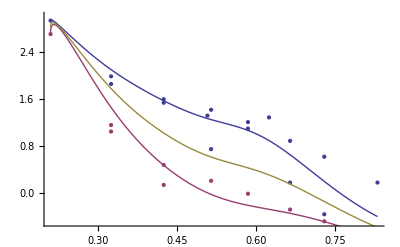

```mathematica
Show[ListPlot[Transpose[{Re[ppdat[[All,1]]],-Im[ppdat[[All,2]]]}]],ListPlot[Transpose[{Re[pndat[[All,1]]],-Im[pndat[[All,2]]]}],PlotStyle->ColorData[1,2]],Plot[{-Im[ppA0[En]],-Im[pnA0[En]],(-Im[ppA0[En]]-Im[pnA0[En]])/2},{En,.210,.831}],PlotRange->{{.21,.831},{-.5,3}}]
```

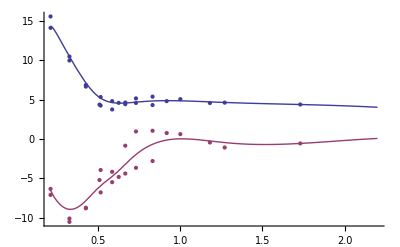

```mathematica
Show[ListPlot[Transpose[{Re[ppdat[[All,1]]],Re[ppdat[[All,3]]]}]],ListPlot[Transpose[{Re[ppdat[[All,1]]],Im[ppdat[[All,3]]]}],PlotStyle->ColorData[1,2]],Plot[{Re[ppβA[En]],Im[ppβA[En]]},{En,.210,2.2}]]
```

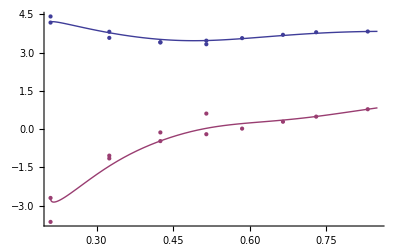

```mathematica
Show[ListPlot[Transpose[{Re[pndat[[All,1]]],Re[pndat[[All,2]]]}]],ListPlot[Transpose[{Re[pndat[[All,1]]],Im[pndat[[All,2]]]}],PlotStyle->ColorData[1,2]],Plot[{Re[pnA0[En]],Im[pnA0[En]]},{En,.210,.85}]]
```

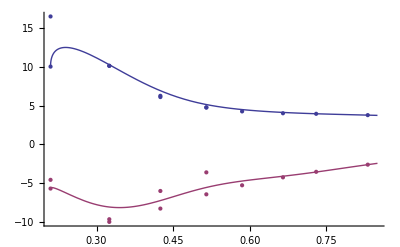

```mathematica
Show[ListPlot[Transpose[{Re[pndat[[All,1]]],Re[pndat[[All,3]]]}]],ListPlot[Transpose[{Re[pndat[[All,1]]],Im[pndat[[All,3]]]}],PlotStyle->ColorData[1,2]],Plot[{Re[pnβA[En]],Im[pnβA[En]]},{En,.210,.85}]]
```